# Prueba Mecanica Int 1 - Fabian Trigo

## Problema 3

#### grafica para visualizar las cosas

```mathematica
m=3.28*^23;
M=2*^30;
G=6.6*^-11;
c=3*^8;
```

```mathematica
U[r_,a_]:=-(G m M /r)(1+a G M / (c^2 r))
```

```mathematica
Manipulate[Plot[U[r,a],{r,1,1000}],{a,-100,100}]
```

#### Con a = 1 tenemos un grafico de un potencial que aumenta al aumentar la distancia, por tanto sabemos que a > 0 De darle una energia total disponible a mercurio creariamos un punto de precesion al comienoz de la grafica si se tratase de un potencial clasico

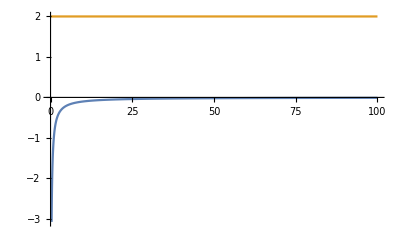

```mathematica
Plot[{-1/r,2},{r,0,100}]
```

#### Aproach para el problema: Calcular el momento angular y demostrar que este no se conserva, osea existe un torque externo